```mathematica
Integrate[2*Exp[-beta*x^2/2],{x,0,Infinity}]
```

ConditionalExpression[(√(2 π))/(√beta),Re[beta]>0]

```mathematica
Plaq = Sqrt[beta/(2 Pi)] Integrate[ 2*Cos[x]*Exp[-beta*x^2/2],{x,0,Infinity}]
```

ConditionalExpression[ⅇ^(-1/2/beta),Re[beta]>0]

```mathematica
sigmaNC[beta_]:=- Log[Sqrt[beta/(2 Pi)] Integrate[ 2*Cos[x]*Exp[-beta*x^2/2],{x,0,Infinity}]]
```

```mathematica
lengthNC[beta_] := 1/Sqrt[sigmaNC[beta]]
```

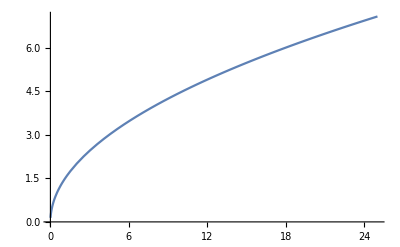

```mathematica
plotStringNC = Plot[lengthNC[beta],{beta,0.01,25}]
```

```mathematica
Integrate[Exp[-beta*(1 -Cos[ x])],{x,0,Pi}]
```

ⅇ^-beta π BesselI[0,beta]

```mathematica
avPlaq[beta_]:=(1.0/( ⅇ^-beta π BesselI[0,beta]))* Integrate[Cos[x]*Exp[-beta*(1 -Cos[ x])],{x,0,Pi}]
```

```mathematica
avPlaq[6.0]
```

0.912359-3.11528×10^-16 ⅈ

```mathematica
0.9123593043529148-3.115281446568006*^-16 ⅈ  
0.91923/0.9123593043529148
```

0.912359-3.11528×10^-16 ⅈ

1.00753

```mathematica
avPlaq[1.8]
```

0.66204-6.968×10^-17 ⅈ

```mathematica
avPlaq[2.0]
```

0.697775-7.97383×10^-17 ⅈ

```mathematica
avPlaq[4.0]
avPlaq[8.0]
avPlaq[10.0]
```

0.863523-1.92054×10^-16 ⅈ

0.935235-4.32592×10^-16 ⅈ

0.9486-1.10848×10^-15 ⅈ

```mathematica
0.9485998259548476-1.1084765214472514*^-15 ⅈ
```

0.9486-1.10848×10^-15 ⅈ

```mathematica
(* sigmaC[beta_]:=- Log[(1.0/(2 ⅇ^-beta π BesselI[0,beta]))* Integrate[2 Cos[x]*Exp[-beta*(1 -Cos[ x])],{x,0,Pi}]]
lengthC[beta_] := 1/Sqrt[sigmaC[beta]]
 *)
```

```mathematica
lengthC[beta_] := 1/Sqrt[- Log[avPlaq[beta]]]
```

```mathematica
lengthC[7.2]
```

3.65036-1.00688×10^-14 ⅈ

```mathematica
(* 3.650362952907459-1.0068803496508269*^-14 ⅈ *)
```

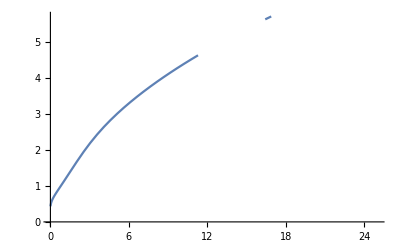

```mathematica
plotStringC = Plot[lengthC[beta],{beta,0.01,25}]
```

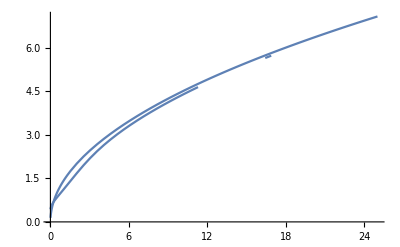

```mathematica
Show[plotStringNC,plotStringC ]
```